```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 275 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,Parallel`Debug`Perfmon`,Parallel`Debug`,System`,Global`}

```mathematica
Clear[r1]
r1 = { - R θ1[t] , R }
```

{-R θ1[t],R}

```mathematica
D[r1, t]
```

{-R θ1'[t],0}

```mathematica
D[r1, t] . D[r1, t]
```

R^2 θ1'[t]^2

```mathematica
Clear[T1]
T1 = 1/2 M (D[r1, t] . D[r1, t] )+ 1/2(1/2 M R^2) θ1'[t]^2
```

3/4 M R^2 θ1'[t]^2

```mathematica
r1[[1]]
```

-R θ1[t]

```mathematica
Clear[r2]
r2 = { r1[[1]]+ 2 R Sin[θ[t]] , R + 2 R Cos[θ[t]] }
```

{2 R Sin[θ[t]]-R θ1[t],R+2 R Cos[θ[t]]}

```mathematica
D[r2, t]
```

{2 R Cos[θ[t]] θ'[t]-R θ1'[t],-2 R Sin[θ[t]] θ'[t]}

```mathematica
D[r2, t] . D[r2, t]
```

4 R^2 Sin[θ[t]]^2 θ'[t]^2+(2 R Cos[θ[t]] θ'[t]-R θ1'[t])^2

```mathematica
D[r2, t] . D[r2, t]  // Expand
```

4 R^2 Cos[θ[t]]^2 θ'[t]^2+4 R^2 Sin[θ[t]]^2 θ'[t]^2-4 R^2 Cos[θ[t]] θ'[t] θ1'[t]+R^2 θ1'[t]^2

```mathematica
D[r2, t] . D[r2, t]  // Expand  // Simplify
```

R^2 (4 θ'[t]^2-4 Cos[θ[t]] θ'[t] θ1'[t]+θ1'[t]^2)

```mathematica
Clear[angles]
angles = 
θ1[t] + θ[t] == θ2[t] - θ[t]
```

θ[t]+θ1[t]==-θ[t]+θ2[t]

```mathematica
Clear[ θ2Replace]
θ2Replace = 
Flatten[Solve[ angles , θ2[t] ] ]
```

{θ2[t]→2 θ[t]+θ1[t]}

```mathematica
D[θ2Replace, t]
```

{θ2'[t]→2 θ'[t]+θ1'[t]}

```mathematica
Clear[T2]
T2 =
1/2 M ( D[r2, t] . D[r2, t]  // Expand  // Simplify  )  +
(1/2 (1/2 M R^2 )( θ2'[t]   //. D[θ2Replace, t] )^2  )  // Expand // Simplify
```

1/4 M R^2 (12 θ'[t]^2-4 (-1+2 Cos[θ[t]]) θ'[t] θ1'[t]+3 θ1'[t]^2)

```mathematica
Clear[T]
T = T1 + T2 ;
T // pdConv
```

1/4 M R^2 (-4 (∂θ(t))/(∂t) (2 cos(θ(t))-1) (∂θ1(t))/(∂t)+12 ((∂θ(t))/(∂t))^2+3 ((∂θ1(t))/(∂t))^2)+3/4 M R^2 ((∂θ1(t))/(∂t))^2

```mathematica
r1
r1[[2]]
r2
r2[[2]]
```

{-R θ1[t],R}

R

{2 R Sin[θ[t]]-R θ1[t],R+2 R Cos[θ[t]]}

R+2 R Cos[θ[t]]

```mathematica
Clear[V]
V = 
M g r1[[2]] + M g r2[[2]]  // Expand // Simplify
```

2 g M R (1+Cos[θ[t]])

```mathematica
Clear[ℒ]
ℒ =  T - V ;
ℒ // pdConv
```

-2 g M R (cos(θ(t))+1)+1/4 M R^2 (-4 (∂θ(t))/(∂t) (2 cos(θ(t))-1) (∂θ1(t))/(∂t)+12 ((∂θ(t))/(∂t))^2+3 ((∂θ1(t))/(∂t))^2)+3/4 M R^2 ((∂θ1(t))/(∂t))^2

```mathematica
Clear[q]
q = { θ[t] , θ1[t] }
```

{θ[t],θ1[t]}

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

M R (2 g Sin[θ[t]]-6 R θ''[t]+R (-1+2 Cos[θ[t]]) θ1''[t])==0
-M R^2 (2 Sin[θ[t]] θ'[t]^2+(1-2 Cos[θ[t]]) θ''[t]+3 θ1''[t])==0

```mathematica
Clear[parameters]
parameters = { 
M-> 20 ,
R -> 0.2 ,
g-> 9.8 
} ;
parameters // TableForm
```

M→20
R→0.2
g→9.8

```mathematica
eqs /. parameters // Expand //  TableForm
```

78.4 Sin[θ[t]]-4.8 θ''[t]-0.8 θ1''[t]+1.6 Cos[θ[t]] θ1''[t]==0
-1.6 Sin[θ[t]] θ'[t]^2-0.8 θ''[t]+1.6 Cos[θ[t]] θ''[t]-2.4 θ1''[t]==0

```mathematica
angles /. t-> 0 
D[angles, t] /. t-> 0
```

θ[0]+θ1[0]==-θ[0]+θ2[0]

θ'[0]+θ1'[0]==-θ'[0]+θ2'[0]

```mathematica
Solve[ θ[0]+θ1[0]==-θ[0]+θ2[0] , θ2[0] ]
```

{{θ2[0]→2 θ[0]+θ1[0]}}

```mathematica
(* REDO these so that they're consistent *)
```

```mathematica
Clear[ics]
ics = { 
θ[0] == 0 ,
θ'[0] == -0.1 ,
θ1[0] == 0 ,
θ1'[0] == 0
} ;
ics // TableForm
```

θ[0]==0
θ'[0]==-0.1
θ1[0]==0
θ1'[0]==0

```mathematica
Clear[solution]
solution[t_]= 
First[NDSolve[ Union[ eqs /. parameters , ics ] , q , { t ,0 , 100 } ]]
```

{θ[t]→InterpolatingFunction[…][t],θ1[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t] ] , { t, 0, 10 } , PlotLabels-> q ]
```

-Graphics-

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{θ[t]→InterpolatingFunction[…][t],θ1[t]→InterpolatingFunction[…][t]}

θ[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

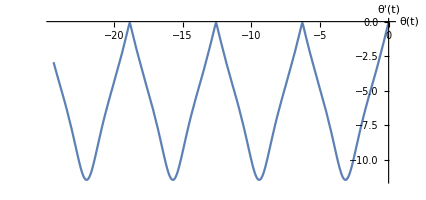

```mathematica
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t, 0, 10 } , AxesLabel-> { q[[1]] , D[q[[1]], t] }  ]
```

```mathematica
solution[t]
solution[t][[2]]
solution[t][[2,2]]
```

{θ[t]→InterpolatingFunction[…][t],θ1[t]→InterpolatingFunction[…][t]}

θ1[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t, 0, tmax } , PlotRange-> All  , AxesLabel-> { q[[2]] , D[q[[2]], t] }]  , { tmax , 0.1 , 10 } ]
```

```mathematica
Clear[com]
com = FirstIntegrals[ ℒ , q , t ] ;
com // TableForm
```

FirstIntegral[θ1]→M R^2 ((-1+2 Cos[θ[t]]) θ'[t]-3 θ1'[t])
FirstIntegral[t]→-1/2 M R (-4 g (1+Cos[θ[t]])-6 R θ'[t]^2+2 R (-1+2 Cos[θ[t]]) θ'[t] θ1'[t]-3 R θ1'[t]^2)

```mathematica
com[[2]]
com[[2,2]] // Expand  // Simplify
```

FirstIntegral[t]→-1/2 M R (-4 g (1+Cos[θ[t]])-6 R θ'[t]^2+2 R (-1+2 Cos[θ[t]]) θ'[t] θ1'[t]-3 R θ1'[t]^2)

-1/2 M R (-4 g (1+Cos[θ[t]])-6 R θ'[t]^2+2 R (-1+2 Cos[θ[t]]) θ'[t] θ1'[t]-3 R θ1'[t]^2)

```mathematica
T+ V // Expand  // FullSimplify
```

1/2 M R (4 g (1+Cos[θ[t]])+6 R θ'[t]^2+2 R (1-2 Cos[θ[t]]) θ'[t] θ1'[t]+3 R θ1'[t]^2)

```mathematica
D[ ℒ , q[[1]] ] 
D[ ℒ , D[q[[1]], t] ]
```

2 g M R Sin[θ[t]]+2 M R^2 Sin[θ[t]] θ'[t] θ1'[t]

1/4 M R^2 (24 θ'[t]-4 (-1+2 Cos[θ[t]]) θ1'[t])

```mathematica
D[ ℒ , q[[2]] ] 
D[ ℒ , D[q[[2]], t] ]  // Expand // Simplify  (* Part B answer *)
```

0

M R^2 ((1-2 Cos[θ[t]]) θ'[t]+3 θ1'[t])